## Discrete Sine and Cosine Transforms

```mathematica
Remove["Global`*"]
```

orthoganility of the basis functions

```mathematica
Table[NIntegrate[Sin[j*x]*Sin[k*x],{x,0,Pi}],{j,1,10},{k,1,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.28251}. NIntegrate obtained -1.73472×10^-17 and 1.80097×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.89595}. NIntegrate obtained -7.37257×10^-17 and 7.8237×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.03094}. NIntegrate obtained 2.75821×10^-16 and 8.51071×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{1.5708,-1.73472×10^-17,-7.37257×10^-17,2.75821×10^-16,1.25767×10^-17,-2.98372×10^-16,-4.16334×10^-17,3.98986×10^-17,1.38778×10^-17,-3.39138×10^-16},{-1.73472×10^-17,1.5708,1.21431×10^-16,-4.85723×10^-17,1.09288×10^-16,2.55004×10^-16,1.42247×10^-16,-1.76942×10^-16,-5.20417×10^-17,1.20563×10^-16},{-7.37257×10^-17,1.21431×10^-16,1.5708,-5.13478×10^-16,7.63278×10^-17,2.43729×10^-16,-2.67147×10^-16,-2.56739×10^-16,2.22045×10^-16,8.73867×10^-17},{2.75821×10^-16,-4.85723×10^-17,-5.13478×10^-16,1.5708,1.73472×10^-18,-3.22659×10^-16,5.75928×10^-16,-2.60209×10^-18,-2.65413×10^-16,-3.31332×10^-16},{1.25767×10^-17,1.09288×10^-16,7.63278×10^-17,1.73472×10^-18,1.5708,-3.32416×10^-16,-4.7011×10^-16,-4.16334×10^-16,1.38778×10^-17,-1.04734×10^-16},{-2.98372×10^-16,2.55004×10^-16,2.43729×10^-16,-3.22659×10^-16,-3.32416×10^-16,1.5708,-8.50015×10^-17,2.498×10^-16,1.43982×10^-16,-5.67255×10^-16},{-4.16334×10^-17,1.42247×10^-16,-2.67147×10^-16,5.75928×10^-16,-4.7011×10^-16,-8.50015×10^-17,1.5708,-3.31332×10^-16,5.48173×10^-16,7.1991×10^-17},{3.98986×10^-17,-1.76942×10^-16,-2.56739×10^-16,-2.60209×10^-18,-4.16334×10^-16,2.498×10^-16,-3.31332×10^-16,1.5708,-3.57353×10^-16,-5.41234×10^-16},{1.38778×10^-17,-5.20417×10^-17,2.22045×10^-16,-2.65413×10^-16,1.38778×10^-17,1.43982×10^-16,5.48173×10^-16,-3.57353×10^-16,1.5708,-1.04083×10^-16},{-3.39138×10^-16,1.20563×10^-16,8.73867×10^-17,-3.31332×10^-16,-1.04734×10^-16,-5.67255×10^-16,7.1991×10^-17,-5.41234×10^-16,-1.04083×10^-16,1.5708}}

As one can see, the value of the integral is (almost) zero, other than in the case j==k, in which case we get the normalization factor N.

normalization factor N

```mathematica
NormFactor = 1/NIntegrate[Sin[x]*Sin[x],{x,0,Pi}]
```

0.63662

just to confirm that the normalization factor is in fact independent of k/j

```mathematica
Table[1/NIntegrate[Sin[k*x]*Sin[k*x],{x,0,Pi}],{k,1,10}]
```

{0.63662,0.63662,0.63662,0.63662,0.63662,0.63662,0.63662,0.63662,0.63662,0.63662}

Similarly, as shown below, the Cosine basis functions also form an orthogonal basis set. We can see that the value of the integral is again (almost) zero in the case j!=k and in the case when j == k, it is the normalization factor

```mathematica
Table[NIntegrate[Cos[j*x]*Cos[k*x],{x,0,Pi}],{j,1,10},{k,1,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.202437}. NIntegrate obtained 1.89085×10^-16 and 1.0298×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.74884}. NIntegrate obtained -4.51028×10^-16 and 1.19323×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {5.6345×10^-8}. NIntegrate obtained 5.89806×10^-17 and 7.90925×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{1.5708,1.89085×10^-16,-4.51028×10^-16,5.89806×10^-17,-2.87964×10^-16,-3.46945×10^-18,-5.27356×10^-16,2.94903×10^-17,-9.54098×10^-17,2.32019×10^-16},{1.89085×10^-16,1.5708,-5.55112×10^-17,-1.94289×10^-16,-9.71445×10^-17,6.93889×10^-18,8.23994×10^-17,-3.1572×10^-16,-7.02563×10^-17,-1.36176×10^-16},{-4.51028×10^-16,-5.55112×10^-17,1.5708,-7.63278×10^-17,-2.42861×10^-16,1.11022×10^-16,-9.75782×10^-17,2.08167×10^-17,-4.84855×10^-16,1.2837×10^-16},{5.89806×10^-17,-1.94289×10^-16,-7.63278×10^-17,1.5708,1.51788×10^-16,-1.249×10^-16,1.40513×10^-16,-1.59942×10^-15,1.31839×10^-16,2.86229×10^-17},{-2.87964×10^-16,-9.71445×10^-17,-2.42861×10^-16,1.51788×10^-16,1.5708,8.32667×10^-17,8.50015×10^-17,1.72497×10^-16,-2.63678×10^-16,4.63605×10^-16},{-3.46945×10^-18,6.93889×10^-18,1.11022×10^-16,-1.249×10^-16,8.32667×10^-17,1.5708,5.10442×10^-16,-5.45571×10^-16,3.82507×10^-16,-6.47052×10^-16},{-5.27356×10^-16,8.23994×10^-17,-9.75782×10^-17,1.40513×10^-16,8.50015×10^-17,5.10442×10^-16,1.5708,-1.1241×10^-15,6.37945×10^-16,1.80411×10^-16},{2.94903×10^-17,-3.1572×10^-16,2.08167×10^-17,-1.59942×10^-15,1.72497×10^-16,-5.45571×10^-16,-1.1241×10^-15,1.5708,-2.08167×10^-17,-1.83881×10^-15},{-9.54098×10^-17,-7.02563×10^-17,-4.84855×10^-16,1.31839×10^-16,-2.63678×10^-16,3.82507×10^-16,6.37945×10^-16,-2.08167×10^-17,1.5708,1.5838×10^-15},{2.32019×10^-16,-1.36176×10^-16,1.2837×10^-16,2.86229×10^-17,4.63605×10^-16,-6.47052×10^-16,1.80411×10^-16,-1.83881×10^-15,1.5838×10^-15,1.5708}}

```mathematica
Table[1/NIntegrate[Cos[k*x]*Cos[k*x],{x,0,Pi}],{k,1,10}]
```

{0.63662,0.63662,0.63662,0.63662,0.63662,0.63662,0.63662,0.63662,0.63662,0.63662}

## x^2

the first ten coefficients b_k for x^2 when written in terms of the sine and cosine basis functions

```mathematica
xSqSinCoeffs = NormFactor*Table[NIntegrate[x^2*Sin[k*x],{x,0,Pi}],
{k,1,10}]
```

{3.73671,-3.14159,2.00008,-1.5708,1.23627,-1.0472,0.890174,-0.785398,0.694639,-0.628319}

```mathematica
xSqCosCoeffs = NormFactor*Table[NIntegrate[x^2*Cos[k*x],{x,0,Pi}],{k,0,10}]
```

{6.57974,-4.,1.,-0.444444,0.25,-0.16,0.111111,-0.0816327,0.0625,-0.0493827,0.04}

reconstructing the function x^2 using the first ten terms of the sine and cosine basis functions

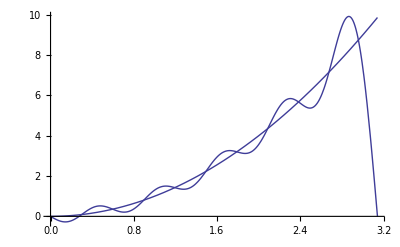

```mathematica
Show[Plot[Sum[xSqSinCoeffs[[i]]*Sin[i*x],{i,1,10}],{x,0,Pi}],Plot[x^2,{x,0,Pi}]]
```

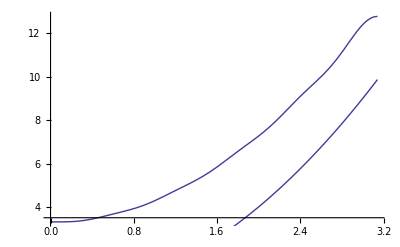

```mathematica
Show[Plot[Sum[xSqCosCoeffs[[i]]*Cos[(i-1)*x],{i,1,11}],{x,0,Pi}],Plot[x^2,{x,0,Pi}]]
```

## x^3

the first ten coefficients b_k for x^3 when written in terms of the sine and cosine basis functions

```mathematica
xCuSinCoeffs = NormFactor*Table[NIntegrate[x^3*Sin[k*x],{x,0,Pi}],
{k,1,10}]

xCuCosCoeffs = NormFactor*Table[NIntegrate[x^3*Cos[k*x],{x,0,Pi}],{k,0,10}]
```

{7.73921,-8.3696,6.13529,-4.7473,3.85184,-3.23431,2.7849,-2.44396,2.17678,-1.96192}

{15.5031,-11.2101,4.71239,-2.00008,1.1781,-0.741759,0.523599,-0.381503,0.294524,-0.231546,0.188496}

reconstructing the function x^3 using the first ten terms of the sine and cosine basis functions

```mathematica
Show[Plot[Sum[xSqSinCoeffs[[i]]*Sin[i*x],{i,1,10}],{x,0,Pi}],Plot[x^2,{x,0,Pi}]]
Show[Plot[Sum[xSqCosCoeffs[[i]]*Cos[(i-1)*x],{i,1,11}],{x,0,Pi}],Plot[x^2,{x,0,Pi}]]
```

-Graphics-

-Graphics-

## exp(-a(x-b)^2)

the first ten coefficients b_k for exp(-a(x-b)^2) when written in terms of the sine and cosine basis functions

```mathematica
a=1; b=0;
nveExpSinCoeffs = 
NormFactor*Table[NIntegrate[Exp[-a*(x-b)^2]*Sin[k*x],{x,0,Pi}],{k,1,10}]

nveExpCosCoeffs = NormFactor*Table[NIntegrate[Exp[-a*(x-b)^2]*Cos[k*x],{x,0,Pi}],{k,0,10}]
```

{0.270205,0.342551,0.272634,0.191837,0.142022,0.113488,0.0952546,0.082343,0.0726335,0.0650182}

{0.564185,0.439396,0.207549,0.0594694,0.0103298,0.00109239,0.0000668262,5.09913×10^-6,-1.99182×10^-6,1.76635×10^-6,-1.52352×10^-6}

reconstructing the function exp(-a(x-b)^2) using the first ten terms of the sine and cosine basis functions

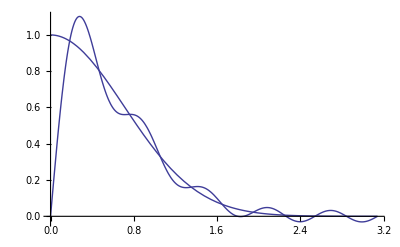

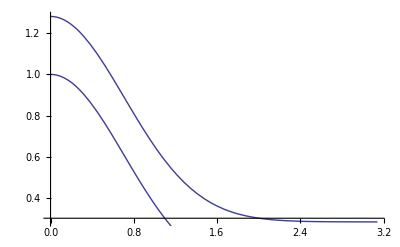

```mathematica
Show[Plot[Sum[nveExpSinCoeffs[[i]]*Sin[i*x],{i,1,10}],{x,0,Pi}],Plot[Exp[-a*(x-b)^2],{x,0,Pi}]]
Show[Plot[Sum[nveExpCosCoeffs[[i]]*Cos[(i-1)*x],{i,1,11}],{x,0,Pi}],Plot[Exp[-a*(x-b)^2],{x,0,Pi}]]
```

## exp(+a(x-b)^2)

the first ten coefficients b_k for exp(a(x-b)^2) when written in terms of the sine and cosine basis functions

```mathematica
a=1; b=0;
pveExpSinCoeffs =NormFactor*Table[NIntegrate[Exp[a*(x-b)^2]*Sin[k*x],{x,0,Pi}],{k,1,10}]

pveExpCosCoeffs =NormFactor*Table[NIntegrate[Exp[a*(x-b)^2]*Cos[k*x],{x,0,Pi}],{k,0,10}]
```

{363.151,-648.555,839.383,-947.206,995.822,-1004.51,989.329,-959.845,923.377,-883.482}

{2079.92,-2006.71,1828.06,-1604.61,1379.52,-1174.72,997.889,-849.265,725.932,-624.046,539.847}

reconstructing the function exp(a(x-b)^2) using the first ten terms of the sine and cosine basis functions

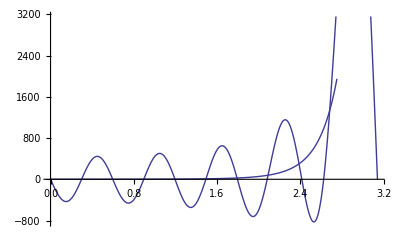

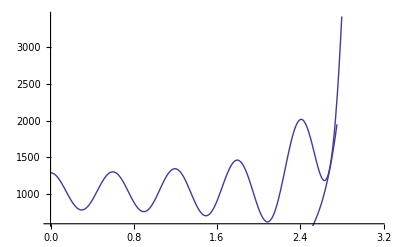

```mathematica
Show[Plot[Sum[pveExpSinCoeffs[[i]]*Sin[i*x],{i,1,10}],{x,0,Pi}],Plot[Exp[a*(x-b)^2],{x,0,Pi}]]
Show[Plot[Sum[pveExpCosCoeffs[[i]]*Cos[(i-1)*x],{i,1,11}],{x,0,Pi}],Plot[Exp[a*(x-b)^2],{x,0,Pi}]]
```

## unit step-function

the first ten coefficients b_k for the unit-step function when written in terms of the sine and cosine basis functions

```mathematica
L=1;
stepFnSinCoeffs =NormFactor*Table[NIntegrate[(1/L)*Sin[k*x],{x,0,L}],{k,1,10}]
stepFnCosCoeffs =NormFactor*Table[NIntegrate[(1/L)*Cos[k*x],{x,0,L}],{k,0,10}]
```

{0.292653,0.450774,0.42229,0.263186,0.091207,0.00422606,0.0223815,0.091156,0.135185,0.117079}

{0.63662,0.535697,0.289438,0.0299466,-0.120449,-0.122094,-0.0296469,0.0597501,0.0787306,0.0291514,-0.0346335}

reconstructing the unit-step function using the first ten terms of the sine and cosine basis functions

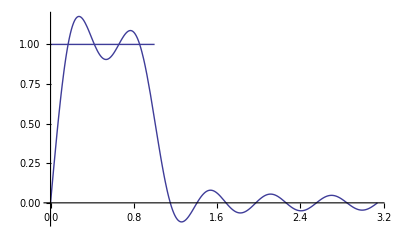

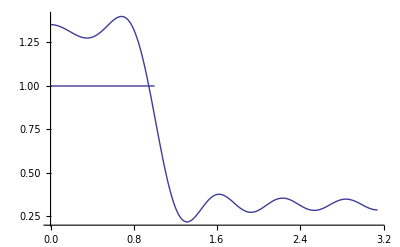

```mathematica
Show[Plot[Sum[stepFnSinCoeffs[[i]]*Sin[i*x],{i,1,10}],{x,0,Pi}],Plot[1/L,{x,0,L}]]
Show[Plot[Sum[stepFnCosCoeffs[[i]]*Cos[(i-1)*x],{i,1,11}],{x,0,Pi}],Plot[1/L,{x,0,L}]]
```